```mathematica
eye = {{1,0},{0,1}}
zero = {{0,0},{0,0}}
(*θ = Pi/2*)
R[θ_] :={{Cos[θ], -Sin[θ]},{Sin[θ], Cos[θ]}}
L [θ_] := ArrayFlatten[{{2*eye, -R[θ], -eye}, {-Transpose[R[θ]], 2*eye, -eye}, {-eye, -eye, 2*eye}}]
```

{{1,0},{0,1}}

{{0,0},{0,0}}

```mathematica
P[θ_] := Simplify[Refine[PseudoInverse[L[θ]],{ Element[θ, Reals], Element[θ, Interval[{0, 2*Pi}]]}]]
```

```mathematica
B[θ_] := ArrayFlatten[{{eye, -R[θ], zero}, {eye, zero, -eye}, {zero, eye, -eye}}]
```

2/3

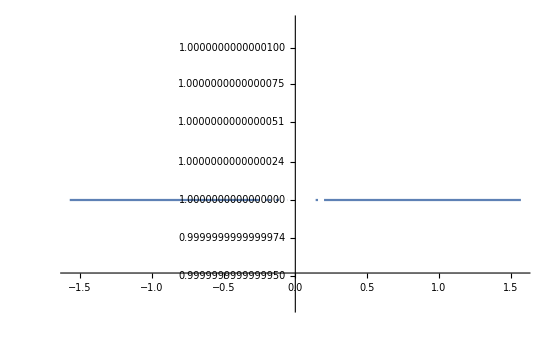

```mathematica
F[s_] :=Norm[Simplify[ B[s].P[s] .Transpose[B[s]]][[1;;2, 1;;2]]]
F[0]
Plot[F[x],{x,-Pi/2, Pi/2}, Exclusions->None]
```

```mathematica
MatrixForm[%44]
```

(-1/2 (-3+Cos[s]+2 Cos[s-x]) Csc[x/2]^2 | 0 | -Cos[s/2] Csc[x/2] Sin[(s-x)/2] | Csc[x/2] Sin[s/2] Sin[(s-x)/2] | Cos[s/2] Csc[x/2] Sin[(s-x)/2] | -Csc[x/2] Sin[s/2] Sin[(s-x)/2]
0 | -1/2 (-3+Cos[s]+2 Cos[s-x]) Csc[x/2]^2 | -Csc[x/2] Sin[s/2] Sin[(s-x)/2] | -Cos[s/2] Csc[x/2] Sin[(s-x)/2] | Csc[x/2] Sin[s/2] Sin[(s-x)/2] | Cos[s/2] Csc[x/2] Sin[(s-x)/2]
-Cos[s/2] Csc[x/2] Sin[(s-x)/2] | -Csc[x/2] Sin[s/2] Sin[(s-x)/2] | 1 | 0 | 0 | 0
Csc[x/2] Sin[s/2] Sin[(s-x)/2] | -Cos[s/2] Csc[x/2] Sin[(s-x)/2] | 0 | 1 | 0 | 0
Cos[s/2] Csc[x/2] Sin[(s-x)/2] | Csc[x/2] Sin[s/2] Sin[(s-x)/2] | 0 | 0 | 1 | 0
-Csc[x/2] Sin[s/2] Sin[(s-x)/2] | Cos[s/2] Csc[x/2] Sin[(s-x)/2] | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[%29]
```

(1. | 2.18159×10^-14 | -7.91589×10^-14 | -4.61853×10^-14 | 2.28706×10^-14 | 3.55271×10^-14
-1.55778×10^-14 | 1. | 2.84217×10^-14 | 4.36318×10^-14 | 7.10543×10^-15 | -5.55112×10^-16
-1.88738×10^-14 | -3.64639×10^-14 | 1. | 3.73035×10^-14 | -5.68434×10^-14 | -4.08562×10^-14
8.87485×10^-15 | 5.38458×10^-14 | -8.88178×10^-15 | 1. | 1.59872×10^-14 | -5.68434×10^-14
8.75966×10^-14 | 4.1446×10^-14 | 0. | -3.19744×10^-14 | 1. | 3.55271×10^-14
-2.26902×10^-14 | -3.33067×10^-16 | 1.24345×10^-14 | -5.68434×10^-14 | -2.13163×10^-14 | 1.)

```mathematica
MatrixForm[{{2/3,0,1/3,0,-1/3,0},{0,2/3,0,1/3,0,-1/3},{1/3,0,2/3,0,1/3,0},{0,1/3,0,2/3,0,1/3},{-1/3,0,1/3,0,2/3,0},{0,-1/3,0,1/3,0,2/3}}]
```

(2/3 | 0 | 1/3 | 0 | -1/3 | 0
0 | 2/3 | 0 | 1/3 | 0 | -1/3
1/3 | 0 | 2/3 | 0 | 1/3 | 0
0 | 1/3 | 0 | 2/3 | 0 | 1/3
-1/3 | 0 | 1/3 | 0 | 2/3 | 0
0 | -1/3 | 0 | 1/3 | 0 | 2/3)

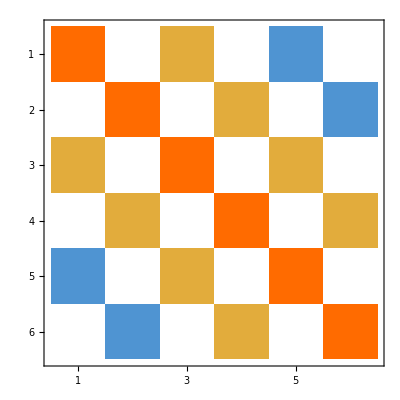

```mathematica
MatrixPlot[{{2/3,0,1/3,0,-1/3,0},{0,2/3,0,1/3,0,-1/3},{1/3,0,2/3,0,1/3,0},{0,1/3,0,2/3,0,1/3},{-1/3,0,1/3,0,2/3,0},{0,-1/3,0,1/3,0,2/3}}]
```

```mathematica
""
```

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[B[s]] MatrixForm[%19]
```

(1/2 | -1/2 Cot[s/2] | 1/2 | 1/2 Cot[s/2] | -1/2 | -1/2 Cot[s/2]
1/2 Cot[s/2] | 1/2 | -1/2 Cot[s/2] | 1/2 | 1/2 Cot[s/2] | -1/2
1/2 | -1/2 Cot[s/2] | -1/2 | 1/2 Cot[s/2] | 1/2 | -1/2 Cot[s/2]
1/2 Cot[s/2] | 1/2 | -1/2 Cot[s/2] | -1/2 | 1/2 Cot[s/2] | 1/2
1/2 | -1/2 Cot[s/2] | -1/2 | 1/2 Cot[s/2] | -1/2 | -1/2 Cot[s/2]
1/2 Cot[s/2] | 1/2 | -1/2 Cot[s/2] | -1/2 | 1/2 Cot[s/2] | -1/2) (1 | 0 | -Cos[s] | Sin[s] | 0 | 0
0 | 1 | -Sin[s] | -Cos[s] | 0 | 0
1 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | -1)

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[%13]
```

(1. | 2.18159×10^-14 | -7.91589×10^-14 | -4.61853×10^-14 | 2.28706×10^-14 | 3.55271×10^-14
-1.55778×10^-14 | 1. | 2.84217×10^-14 | 4.36318×10^-14 | 7.10543×10^-15 | -5.55112×10^-16
-1.88738×10^-14 | -3.64639×10^-14 | 1. | 3.73035×10^-14 | -5.68434×10^-14 | -4.08562×10^-14
8.87485×10^-15 | 5.38458×10^-14 | -8.88178×10^-15 | 1. | 1.59872×10^-14 | -5.68434×10^-14
8.75966×10^-14 | 4.1446×10^-14 | 0. | -3.19744×10^-14 | 1. | 3.55271×10^-14
-2.26902×10^-14 | -3.33067×10^-16 | 1.24345×10^-14 | -5.68434×10^-14 | -2.13163×10^-14 | 1.)

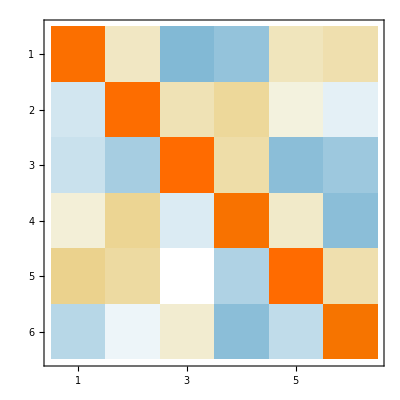

```mathematica
MatrixPlot[%13]
```

```mathematica
MatrixForm[%13]
```

(1. | 2.18159×10^-14 | -7.91589×10^-14 | -4.61853×10^-14 | 2.28706×10^-14 | 3.55271×10^-14
-1.55778×10^-14 | 1. | 2.84217×10^-14 | 4.36318×10^-14 | 7.10543×10^-15 | -5.55112×10^-16
-1.88738×10^-14 | -3.64639×10^-14 | 1. | 3.73035×10^-14 | -5.68434×10^-14 | -4.08562×10^-14
8.87485×10^-15 | 5.38458×10^-14 | -8.88178×10^-15 | 1. | 1.59872×10^-14 | -5.68434×10^-14
8.75966×10^-14 | 4.1446×10^-14 | 0. | -3.19744×10^-14 | 1. | 3.55271×10^-14
-2.26902×10^-14 | -3.33067×10^-16 | 1.24345×10^-14 | -5.68434×10^-14 | -2.13163×10^-14 | 1.)

```mathematica
MatrixForm[%11]
```

(0.100004 | 6.37744×10^-6 | 0.899993 | -6.23334×10^-6 | -0.899997 | 7.13061×10^-6
-2.98879×10^-8 | 0.100007 | -1.44501×10^-7 | 0.899997 | -1.18051×10^-6 | -0.900001
2.91226×10^-7 | 2.84215×10^-6 | 0.999996 | -4.71754×10^-6 | 3.8147×10^-6 | 3.25883×10^-6
6.67004×10^-7 | 1.95083×10^-6 | 8.72329×10^-7 | 0.999996 | 3.72413×10^-7 | 0.
-4.10596×10^-6 | -4.16709×10^-6 | 3.8147×10^-6 | 2.14766×10^-6 | 1. | -4.50366×10^-6
2.30177×10^-7 | -5.76567×10^-6 | 1.48355×10^-6 | 0. | 1.08621×10^-6 | 1.)

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[%45]
```

(1. | 2.18159×10^-14 | -7.91589×10^-14 | -4.61853×10^-14 | 2.28706×10^-14 | 3.55271×10^-14
-1.55778×10^-14 | 1. | 2.84217×10^-14 | 4.36318×10^-14 | 7.10543×10^-15 | -5.55112×10^-16
-1.88738×10^-14 | -3.64639×10^-14 | 1. | 3.73035×10^-14 | -5.68434×10^-14 | -4.08562×10^-14
8.87485×10^-15 | 5.38458×10^-14 | -8.88178×10^-15 | 1. | 1.59872×10^-14 | -5.68434×10^-14
8.75966×10^-14 | 4.1446×10^-14 | 0. | -3.19744×10^-14 | 1. | 3.55271×10^-14
-2.26902×10^-14 | -3.33067×10^-16 | 1.24345×10^-14 | -5.68434×10^-14 | -2.13163×10^-14 | 1.)

```mathematica
MatrixPlot[%43]
```

-Graphics-

```mathematica
MatrixForm[{{2/3,0,1/3,0,-1/3,0},{0,2/3,0,1/3,0,-1/3},{1/3,0,2/3,0,1/3,0},{0,1/3,0,2/3,0,1/3},{-1/3,0,1/3,0,2/3,0},{0,-1/3,0,1/3,0,2/3}}]
```

(2/3 | 0 | 1/3 | 0 | -1/3 | 0
0 | 2/3 | 0 | 1/3 | 0 | -1/3
1/3 | 0 | 2/3 | 0 | 1/3 | 0
0 | 1/3 | 0 | 2/3 | 0 | 1/3
-1/3 | 0 | 1/3 | 0 | 2/3 | 0
0 | -1/3 | 0 | 1/3 | 0 | 2/3)

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

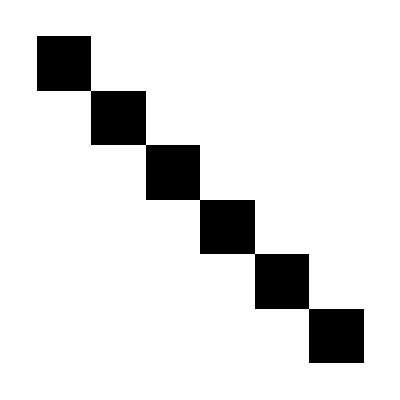

```mathematica
ArrayPlot[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

```mathematica
MatrixForm[%28]
```

(3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0
0 | 3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0
-1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0
0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2
0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2 | 0
0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2)

```mathematica
TableForm[%28]
```

3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0
0 | 3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0
-1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0
0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2
0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2 | 0
0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2

```mathematica
MatrixForm[{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[%18]
```

(3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0
0 | 3/4 Csc[θ/2]^2 | 0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0
-1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0
0 | -1/4 Cos[θ] (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2
0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2 | 0
0 | 0 | 0 | -1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2)

```mathematica
MatrixForm[%11]
```

(3/4 Csc[θ/2]^2 | 0 | 1/4 (1+2 Cos[θ]) Csc[θ/2]^2 | -Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2 | -1/2 Cot[θ/2]
0 | 3/4 Csc[θ/2]^2 | Cot[θ/2] | 1/4 (1+2 Cos[θ]) Csc[θ/2]^2 | 1/2 Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2
1/4 (1+2 Cos[θ]) Csc[θ/2]^2 | Cot[θ/2] | 3/4 Csc[θ/2]^2 | 0 | 1/4 (2+Cos[θ]) Csc[θ/2]^2 | 1/2 Cot[θ/2]
-Cot[θ/2] | 1/4 (1+2 Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2 | -1/2 Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2
1/4 (2+Cos[θ]) Csc[θ/2]^2 | 1/2 Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2 | -1/2 Cot[θ/2] | 3/4 Csc[θ/2]^2 | 0
-1/2 Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2 | 1/2 Cot[θ/2] | 1/4 (2+Cos[θ]) Csc[θ/2]^2 | 0 | 3/4 Csc[θ/2]^2)

```mathematica
MatrixForm[{{3/2,0,1/2,-1,1,-1/2},{0,3/2,1,1/2,1/2,1},{1/2,1,3/2,0,1,1/2},{-1,1/2,0,3/2,-1/2,1},{1,1/2,1,-1/2,3/2,0},{-1/2,1,1/2,1,0,3/2}}]
```

(3/2 | 0 | 1/2 | -1 | 1 | -1/2
0 | 3/2 | 1 | 1/2 | 1/2 | 1
1/2 | 1 | 3/2 | 0 | 1 | 1/2
-1 | 1/2 | 0 | 3/2 | -1/2 | 1
1 | 1/2 | 1 | -1/2 | 3/2 | 0
-1/2 | 1 | 1/2 | 1 | 0 | 3/2)

```mathematica
MatrixForm[{{2,0,0,1,-1,0},{0,2,-1,0,0,-1},{0,-1,2,0,-1,0},{1,0,0,2,0,-1},{-1,0,-1,0,2,0},{0,-1,0,-1,0,2}}]
```

(2 | 0 | 0 | 1 | -1 | 0
0 | 2 | -1 | 0 | 0 | -1
0 | -1 | 2 | 0 | -1 | 0
1 | 0 | 0 | 2 | 0 | -1
-1 | 0 | -1 | 0 | 2 | 0
0 | -1 | 0 | -1 | 0 | 2)

```mathematica
MatrixForm[%10]
```

(-9/(-19+Cos[2 θ]) | (3 Sin[θ])/(-19+Cos[2 θ]) | -(2+6 Cos[θ]+Cos[2 θ])/(-19+Cos[2 θ]) | ((7+2 Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11+6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | ((5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ])
-(3 Sin[θ])/(-19+Cos[2 θ]) | -9/(-19+Cos[2 θ]) | -((7+2 Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(2+6 Cos[θ]+Cos[2 θ])/(-19+Cos[2 θ]) | -((5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11+6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ]))
-(2-6 Cos[θ]+Cos[2 θ])/(-19+Cos[2 θ]) | -((-7+2 Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -9/(-19+Cos[2 θ]) | (3 Sin[θ])/(-19+Cos[2 θ]) | -(11-6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | -((-5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ])
((-7+2 Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(2-6 Cos[θ]+Cos[2 θ])/(-19+Cos[2 θ]) | -(3 Sin[θ])/(-19+Cos[2 θ]) | -9/(-19+Cos[2 θ]) | ((-5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11-6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ]))
-(11-6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | -((-5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11+6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | ((5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -15/(-19+Cos[2 θ]) | (5 Sin[θ])/(-19+Cos[2 θ])
((-5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11-6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | -((5+Cos[θ]) Sin[θ])/(-19+Cos[2 θ]) | -(11+6 Cos[θ]+Cos[2 θ])/(2 (-19+Cos[2 θ])) | -(5 Sin[θ])/(-19+Cos[2 θ]) | -15/(-19+Cos[2 θ]))

```mathematica
MatrixForm[L]
```

(2 | 0 | -Cos[θ] | Sin[θ] | -1 | 0
0 | 2 | -Sin[θ] | -Cos[θ] | 0 | -1
Cos[θ] | Sin[θ] | 2 | 0 | -1 | 0
-Sin[θ] | Cos[θ] | 0 | 2 | 0 | -1
-1 | 0 | -1 | 0 | 2 | 0
0 | -1 | 0 | -1 | 0 | 2)

```mathematica
MatrixForm[L]
```

(2 | 0 | 0 | 1 | -1 | 0
0 | 2 | -1 | 0 | 0 | -1
0 | 1 | 2 | 0 | -1 | 0
-1 | 0 | 0 | 2 | 0 | -1
-1 | 0 | -1 | 0 | 2 | 0
0 | -1 | 0 | -1 | 0 | 2)

```mathematica
Dimensions[L]
```

{3,3,2,2}

```mathematica
ArrayDepth[L]
```

4

```mathematica
Flatten[L]
```

{2,0,0,2,0,1,-1,0,-1,0,0,-1,0,1,-1,0,2,0,0,2,-1,0,0,-1,-1,0,0,-1,-1,0,0,-1,2,0,0,2}

```mathematica
P[x]
```

{{3/4 Csc[x/2]^2,0,1/4 (1+2 Cos[x]) Csc[x/2]^2,-Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2,-1/2 Cot[x/2]},{0,3/4 Csc[x/2]^2,Cot[x/2],1/4 (1+2 Cos[x]) Csc[x/2]^2,1/2 Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2},{1/4 (1+2 Cos[x]) Csc[x/2]^2,Cot[x/2],3/4 Csc[x/2]^2,0,1/4 (2+Cos[x]) Csc[x/2]^2,1/2 Cot[x/2]},{-Cot[x/2],1/4 (1+2 Cos[x]) Csc[x/2]^2,0,3/4 Csc[x/2]^2,-1/2 Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2},{1/4 (2+Cos[x]) Csc[x/2]^2,1/2 Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2,-1/2 Cot[x/2],3/4 Csc[x/2]^2,0},{-1/2 Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2,1/2 Cot[x/2],1/4 (2+Cos[x]) Csc[x/2]^2,0,3/4 Csc[x/2]^2}}

```mathematica
MatrixForm[%40]
```

(3/4 Csc[x/2]^2 | 0 | 1/4 (1+2 Cos[x]) Csc[x/2]^2 | -Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2 | -1/2 Cot[x/2]
0 | 3/4 Csc[x/2]^2 | Cot[x/2] | 1/4 (1+2 Cos[x]) Csc[x/2]^2 | 1/2 Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2
1/4 (1+2 Cos[x]) Csc[x/2]^2 | Cot[x/2] | 3/4 Csc[x/2]^2 | 0 | 1/4 (2+Cos[x]) Csc[x/2]^2 | 1/2 Cot[x/2]
-Cot[x/2] | 1/4 (1+2 Cos[x]) Csc[x/2]^2 | 0 | 3/4 Csc[x/2]^2 | -1/2 Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2
1/4 (2+Cos[x]) Csc[x/2]^2 | 1/2 Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2 | -1/2 Cot[x/2] | 3/4 Csc[x/2]^2 | 0
-1/2 Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2 | 1/2 Cot[x/2] | 1/4 (2+Cos[x]) Csc[x/2]^2 | 0 | 3/4 Csc[x/2]^2)

```mathematica
MatrixForm[%37]
```

(121.836 | 4.34878×10^-12 | 120.836 | -12.7062 | 121.336 | -6.3531
-2.71128×10^-12 | 121.836 | 12.7062 | 120.836 | 6.3531 | 121.336
120.836 | 12.7062 | 121.836 | 5.45979×10^-12 | 121.336 | 6.3531
-12.7062 | 120.836 | -1.51938×10^-12 | 121.836 | -6.3531 | 121.336
121.336 | 6.3531 | 121.336 | -6.3531 | 121.836 | 4.9077×10^-12
-6.3531 | 121.336 | 6.3531 | 121.336 | -2.06534×10^-12 | 121.836)

```mathematica
MatrixForm[%35]
```

(3/4 Csc[π/40]^2 | 0 | 1/4 (1+2 Cos[π/20]) Csc[π/40]^2 | -Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2 | -1/2 Cot[π/40]
0 | 3/4 Csc[π/40]^2 | Cot[π/40] | 1/4 (1+2 Cos[π/20]) Csc[π/40]^2 | 1/2 Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2
(Csc[π/40]^2 (216+22 √(2 (5+√5))+43 (-1+√5) Csc[π/20]))/(512+352 Cos[π/20]) | Cot[π/40] | 3/4 Csc[π/40]^2 | 0 | (Csc[π/40]^2 (300+11 √(2 (5+√5))+38 (-1+√5) Csc[π/20]))/(512+352 Cos[π/20]) | 1/2 Cot[π/40]
-Cot[π/40] | 1/4 (1+2 Cos[π/20]) Csc[π/40]^2 | 0 | 3/4 Csc[π/40]^2 | -1/2 Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2
1/4 (2+Cos[π/20]) Csc[π/40]^2 | 1/2 Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2 | -1/2 Cot[π/40] | 3/4 Csc[π/40]^2 | 0
-1/2 Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2 | 1/2 Cot[π/40] | 1/4 (2+Cos[π/20]) Csc[π/40]^2 | 0 | 3/4 Csc[π/40]^2)

```mathematica
B[s]
```

{{1,0,-Cos[s],Sin[s],0,0},{0,1,-Sin[s],-Cos[s],0,0},{1,0,0,0,-1,0},{0,1,0,0,0,-1},{0,0,1,0,-1,0},{0,0,0,1,0,-1}}

```mathematica
MatrixForm[{{1,0,-Cos[s],Sin[s],0,0},{0,1,-Sin[s],-Cos[s],0,0},{1,0,0,0,-1,0},{0,1,0,0,0,-1},{0,0,1,0,-1,0},{0,0,0,1,0,-1}}]
```

(1 | 0 | -Cos[s] | Sin[s] | 0 | 0
0 | 1 | -Sin[s] | -Cos[s] | 0 | 0
1 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | -1)